```mathematica
(* create a Gaussian Kernel of radius 1 *)
```

```mathematica
kernel=GaussianMatrix[1]
```

{{0.00987648,0.0796275,0.00987648},{0.0796275,0.641984,0.0796275},{0.00987648,0.0796275,0.00987648}}

```mathematica
(* Visualise the kernel - values increase towards the centre of the matrix*)
```

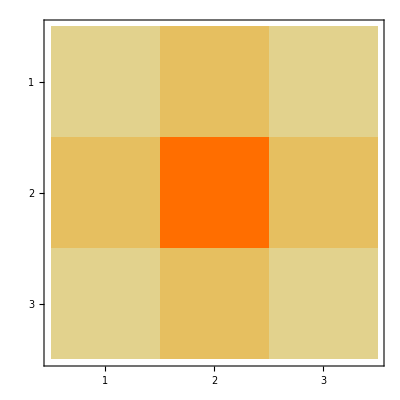

```mathematica
MatrixPlot[kernel]
```

```mathematica
(* Take a random image and apply the kernel to the image at each pixel value *)
```

```mathematica
sun = -Graphics-;
```

```mathematica
new=ImageCorrelate[sun, kernel]
```

-Graphics-

```mathematica
(* Repeat the process up to 100 times *)
```

```mathematica
Manipulate[
Nest[ImageCorrelate[#, kernel]&, sun,n],{n,1,100,1}
]
```